MAD 4401 Computer Project 2
11/1/2019
Group 8- Cristian Dionisi, Nicholas Ionata, Joel Juver, Johnny Li

The problems were individually completely solved by the respective student. 

Statement from Johnny Li:
I develop an interpolating polynomial for the function f(x)=sin(pi*x) at the points (x0, ... , x2) through the traditional method of deriving the  Lagrange pieces  and combining them together. This was checked with the internal Mathematica function for interpolation. The function and interpolating polynomial was then graphed together to compare its accuracy. The absolute error at x=1.4 was take with |f(x)-p(x)|<=error and the error bound was also taken. 
Problem #1 -by Johnny Li
Given Function

```mathematica
f[x_] := Sin[Pi*x]
```

Construct Lagrange Interpolating Polynomial

```mathematica
L0[x_]:=((x-1.25)(x-1.6))/((1-1.25)(1-1.6))
```

```mathematica
L1[x_]:=((x-1)(x-1.6))/((1.25-1)(1.25-1.6))
```

```mathematica
L2[x_]:=((x-1)(x-1.25))/((1.6-1)(1.6-1.25))
```

```mathematica
P2[x_]:=f[1]*L0[x]+f[1.25]*L1[x]+f[1.6]*L2[x]
```

Graph f(x) (blue) and the interpolating polynomial (red) together on the same graph.

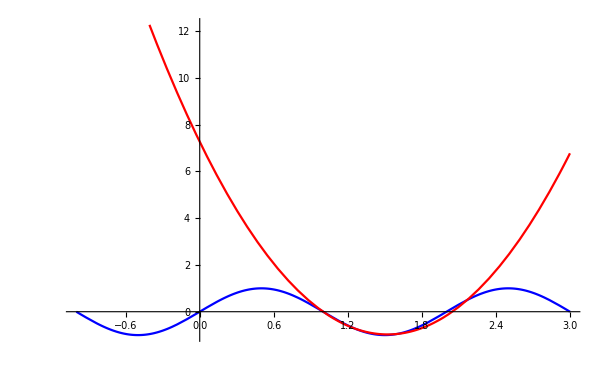

```mathematica
Plot[{f[x],P2[x]},{x,-1,3},PlotStyle->{Blue,Red}]
```

Simplify the Lagrange Polynomials

```mathematica
P2[x]
```

0.+8.08122 (-1.6+x) (-1+x)-4.52884 (-1.25+x) (-1+x)

```mathematica
Expand[P2[x]]
```

7.2689-10.8213 x+3.55238 x^2

Double check with built in function command.

```mathematica
InterpolatingPolynomial[{{1,f[1]},{1.25,f[1.25]},{1.6,f[1.6]}},x]
```

-0.951057+(-1.58509+3.55238 (-1+x)) (-1.6+x)

Matches

```mathematica
Expand[%]
```

7.2689-10.8213 x+3.55238 x^2

Approximate f(1.4),  and  find  the absolute error.

```mathematica
f[1.4]
```

-0.951057

```mathematica
Abs[f[1.4]-P2[1.4]]
```

0.0328285

Error bound for the point  at 1.4.
 [(x-x0)(x-x1)(x-x2)]/(n+1)!  * f^(n+1)(cx)

```mathematica
Abs[((1.4-1)(1.4-1.25)(1.4-1.6)/(2+1)!)*f'''[x]]
```

0.0620126 Abs[Cos[π x]]

Since the max of cos(Pi*x) is 1 then the error bound of the point is: (0.0620126 , 1)

Statement from Joel Juver:
I commentated within the excel file, but I used the dividend-difference table and the general dividend difference formula to construct the interpolating polynomial based on those values in the table. I then plugged in the value that was to be approximated to find the corresponding f(x) value. 
Problem #2 -by Joel Juver

Solution within the attached Excel file.


Statement from Nicholas Ionata:
Number 3 for the project. I used the fit function to calculate the least squares polynomials of degrees 1, 2, and 3. I then calculated error by summing up the differences for each of the data points and the functions. 
Problem #3 -by Nicholas Ionata

{{0,1.},{0.15,1.004},{0.31,1.031},{0.5,1.117},{0.6,1.223},{0.75,1.422}}

0.929514+0.528102 x

1.01134-0.325699 x+1.14733 x^2

1.00044-0.00154099 x-0.0115057 x^2+1.02102 x^3

0.929514+0.528102 x

1.01134-0.325699 x+1.14733 x^2

1.00044-0.00154099 x-0.0115057 x^2+1.02102 x^3

0.0245661

0.000945246

0.000111238

For the data set {{0,1.},{0.15,1.004},{0.31,1.031},{0.5,1.117},{0.6,1.223},{0.75,1.422}}

the first degree least squares polynomial 0.929514+0.528102 x has the error 0.0245661

the second degree least squares polynomial 1.01134-0.325699 x+1.14733 x^2 has the error 0.000945246

the third degree least squares polynomial 1.00044-0.00154099 x-0.0115057 x^2+1.02102 x^3 has the error 0.000111238

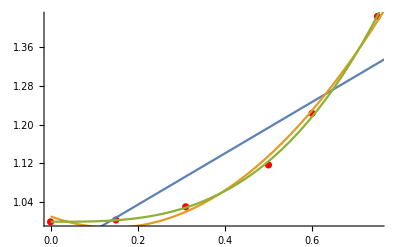

```mathematica
data={{0, 1.0}, {0.15,1.004}, {0.31,1.031}, {0.5,1.117}, {0.6,1.223}, {0.75,1.422}}

polyOne = Fit[data, {1, x}, x] 
polyTwo = Fit[data, {1,x, x^2}, x]
polyThree = Fit[data, {1,x, x^2,x^3},x]

fOne[x_] = polyOne
fTwo[x_] = polyTwo
fThree[x_] = polyThree

Eone = Sum[(data[[i]][[2]] - fOne[data[[i]][[1]]])^2,{i, 1,6}]
Etwo = Sum[(data[[i]][[2]] - fTwo[data[[i]][[1]]])^2,{i, 1,6}]
Ethree = Sum[(data[[i]][[2]] - fThree[data[[i]][[1]]])^2,{i, 1,6}]

Print["For the data set ", data]
Print["the first degree least squares polynomial ", polyOne, " has the error ", Eone]
Print["the second degree least squares polynomial ", polyTwo, " has the error ", Etwo]
Print["the third degree least squares polynomial ", polyThree, " has the error ", Ethree]
Show[ListPlot[data,PlotStyle->Red],Plot[{polyOne, polyTwo, polyThree},{x, 0, 1}]]
```

Statement from Cristian Dionisi:
I used matrix methods to find the least square approximation of the function. Setting alpha equal to b and beta equal to ln(a), I created matrix Ax=B, with matrix A containing 1’s on the first column and Xi’s in the second column, matrix x containing beta and alpha, and matrix B containing Yi’s. Applying A transpose to both sides, and solving the remaining system , I found that alpha = 0.372418 = b and beta = 3.18858 = ln(a), meaning a = 24.25396. This means that the least squares exponential function is y = 24.25396*e^(0.372418*x). The function is plotted with the original points in figure x. Desmos was used to plot the function. 
Problem #4 -by Cristian Dionisi

-Graphics-